```mathematica
ClearAll["Global`*"];Clear[Derivative];
```

```mathematica
SetDirectory["/Users/tosku/Documents/sggs/"]
```

/Users/tosku/Documents/sggs

```mathematica
Import[NotebookDirectory[]<>"lattice.wl"];
```

```mathematica
L=5;
d=2;
pcb=False;
```

```mathematica
lattice=If[pcb,getPCBLattice[L,d],getFreeBoundaryLattice[L,d]];
latticeFile="tests/L5/1.lattice";
OpenRead[latticeFile];
ledgelist=ReadList[latticeFile, {Number,Number,Number}];
Close[latticeFile];
lattice=Graph[listToEdges[{#[[1]],#[[2]]}&/@ledgelist],EdgeWeight->First[{Last[#]&/@ledgelist}]];
Jij[lattice,#]&/@EdgeList[lattice]
```

{1,-1,-1,1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,-1,1,1,1,1,-1,-1,1,-1,-1,1,1,1,1,-1,1,1,-1,1,-1,1,1,-1,-1,1,1}

```mathematica
nV[i_,j_,L_]:=If[pcb,nextVertex[i,j,L],nextVertexFreeBoundary[i,j,L]];
pV[i_,j_,L_]:=If[pcb,previousVertex[i,j,L],previousVertexFreeBoundary[i,j,L]];
```

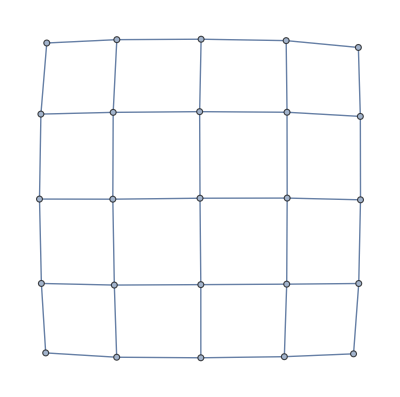

```mathematica
lattice
```

```mathematica
(*Function to map Plaquettes as lists of edges *)
plaquetteOfVertexInPlane[i_,plane_,L_]:=
Fold[If[#1=={},
Append[#1,{i,nV[i,#2,L]}],
If[NumericQ[Last[Last[#1]]],
Append[#1,{Last[Last[#1]],
If[Length[#1]<2,
nV[Last[Last[#1]],#2,L],
pV[Last[Last[#1]],#2,L]
]}
],Append[#1,{Last[Last[#1]],False}]]
]&,{},Join[plane,plane]]
```

```mathematica
isPlaquette[plaquette_]:=Fold[If[#1==True&&NumericQ[First[#2]]&&NumericQ[Last[#2]],True,False]&,True,plaquette]
```

```mathematica
getInternalPlaquettes[L_,d_]:=Select[Sort[Flatten[Map[Function[vl,plaquetteOfVertexInPlane[vl,#,L]&/@Subsets[Range[1,d],{2}]][#]&,Range[1,L^d]],1]],isPlaquette];
```

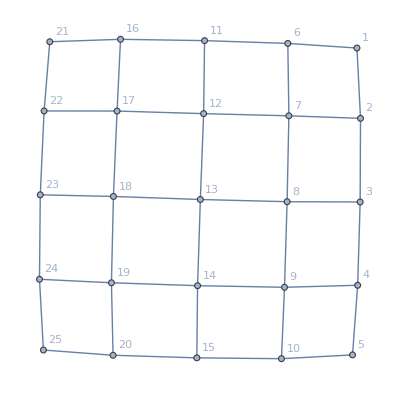

```mathematica
getFreeBoundaryLattice[L,d]//labelVertices
```

```mathematica
(* todo test for all d 
countTest[plaqs_,d_]:=
If[d==2,Length[plaqs]==(L-1)^d,If[d==3,2d(L-1)^d/2+2d*(L-1)^2/2,"no test yet"]]
*)
```

```mathematica
isFrustrated[graph_,cycle_]:= Fold[#1*Jij[graph, Apply[UndirectedEdge,#2]]&,1,cycle]<0;
```

```mathematica
totalFrustration[graph_,cycles_]:=Length[Select[cycles,isFrustrated[graph,#]&]];
totalFrustration[lattice,getInternalPlaquettes[L,d]]
```

8

```mathematica
N[totalFrustration[lattice,getInternalPlaquettes[L,d]]/Length[getInternalPlaquettes[L,d]]]
```

0.5

```mathematica
labelCycles[cycles_]:=MapThread[List,{Range[1,Length[cycles]],cycles}]
```

```mathematica
(* basic subgraphs of a barahona city as edge lists *)
getXNOR[label_]:={{Append[label,1],Append[label,2]},{Append[label,2],Append[label,3]},{Append[label,3],Append[label,1]}};
```

```mathematica
getXOR[label_]:={{Append[label,1],Append[label,4]},{Append[label,4],Append[label,6]},{Append[label,4],Append[label,5]},{Append[label,5],Append[label,6]},{Append[label,5],Append[label,2]},{Append[label,6],Append[label,3]}};
```

```mathematica
addNeighborhoods[na_, nb_]:=Apply[UndirectedEdge,#]&/@Append[Join[na,nb],{Flatten[{Take[First[First[na]],Length[First[First[na]]]-1],3}],Flatten[{Take[First[First[nb]],Length[First[First[nb]]]-1],3}]}];
```

```mathematica
getCompName[component_]:=If[Length[component]>6,
First[First[First[component]]],
Take[First[First[component]],Length[First[First[component]]]-1]
];
```

```mathematica
getFreeVertices[component_]:=
Sort[Complement[Complement[DeleteDuplicates[Flatten[component,1]],
DeleteDuplicates[Select[Flatten[component,1],Count[Flatten[component,1],#]==3&]],DeleteDuplicates[Flatten[Select[component,(Last[First[#]]==3||Last[Last[#]]==3)&&First[#][[2]]≠Last[#][[2]]&],1]]]]]
```

```mathematica
getBiggerFreeVertex[component_]:=
Last[getFreeVertices[component]]
```

```mathematica
addComponents[componentList_]:=Fold[If[Length[#1]==0,#2,Join[#1,Append[#2,{getBiggerFreeVertex[#1],getBiggerFreeVertex[#2]}]]]&,{},componentList]
```

```mathematica
(*plaquetteToBarahonaCity*)
```

```mathematica
edgeListOfBarahonaCity[Lattice_,plaquetteName_,plaquetteEdges_]:=If[isFrustrated[Lattice,plaquetteEdges],
addComponents[Fold[Append[#1,getXOR[{plaquetteName,#2}]]&,{getXNOR[{plaquetteName,1}]},Range[2,Length[plaquetteEdges]-2]]],
addComponents[Fold[Append[#1,getXOR[{plaquetteName,#2}]]&,{},Range[1,Length[plaquetteEdges]-2]]]
]
```

```mathematica
plaquettesToBarahonaCities[lattice_,L_,d_]:=edgeListOfBarahonaCity[lattice,First[#],Last[#]]&/@labelCycles[getInternalPlaquettes[L,d]]
```

```mathematica
cityList=plaquettesToBarahonaCities[lattice,L,d];
```

```mathematica
findAdjacentPlaquette[edge_,plaquettes_]:=Select[labelCycles[plaquettes],Length[Position[#,Reverse[edge]]]≠0||Length[Position[#,edge]]≠0&]
```

```mathematica
intraPlaquetteEdges[plaquettes_,edges_]:=Select[Fold[Append[#1,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],plaquettes]]]&,{},edges],Length[#]>1&]
```

```mathematica
plaquetteToLEdges[plaquetteName_,L_,d_]:=Last[Last[Select[labelCycles[getInternalPlaquettes[L,d]],First[#]==plaquetteName&]]];
```

```mathematica
getCityOfPlaquette[cityList_,plaquetteName_]:=Select[cityList,getCompName[#]==plaquetteName&];
```

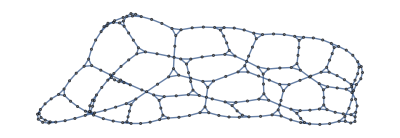

```mathematica
getVertexFromList[cityList_,name_]:=SelectFirst[cityList,First[#]==name&];
getEdgeFromFreeList[freeList_,edge_]:=Fold[Append[#1, getVertexFromList[Complement[freeList,#1],#2]]&,{}, edge]

intraCityEdges[cityList_,cityEdges_]:=Fold[
Append[#1,getEdgeFromFreeList[Complement[Flatten[getFreeVertices[#]&/@cityList,1],Flatten[#1,1]],#2]]
&,{},cityEdges];

boundaryCityEdges[plaquettes_,edges_]:=Append[Last[#],0]&/@Select[Fold[Append[#1,{#2,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],plaquettes]]}]&,{},edges],Length[Last[#]]<2&]

boundaryEdges[plaquettes_,edges_]:=First[#]&/@Select[Fold[Append[#1,{#2,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],plaquettes]]}]&,{},edges],Length[Last[#]]<2&]

boundaryLEdgePlaquetteList[L_,d_,lattice_]:=Select[Fold[Append[#1,{#2,Join[First[#]&/@findAdjacentPlaquette[Apply[List,#2],getInternalPlaquettes[L,d]]]}]&,{},EdgeList[lattice]],Length[Last[#]]<2&]

makeBoundaryCycle[plaquettes_,lattice_]:=edgeListOfBarahonaCity[lattice,0,boundaryEdges[plaquettes,Apply[List,#]&/@EdgeList[lattice]]]

(* Matching graph for pbc lattices
matchingGraphEdgeList[lattice_,L_,d_]:=Join[intraCityEdges[plaquettesToBarahonaCities[lattice,L,d],intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]]]
,Flatten[plaquettesToBarahonaCities[lattice,L,d],1]] *)

JEdges[lattice_,L_,d_]:=If[pcb,
intraCityEdges[
plaquettesToBarahonaCities[lattice,L,d],Join[intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]]]],
intraCityEdges[
Append[plaquettesToBarahonaCities[lattice,L,d],makeBoundaryCycle[getInternalPlaquettes[L,d],lattice]],Join[intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]],boundaryCityEdges[getInternalPlaquettes[L,d],edgesToList[EdgeList[lattice]]]]]
]

(* Matching dual graph for 2d free boundary lattice ]*)
matchingGraphEdgeList[lattice_,L_,d_]:=
If[pcb,
Join[intraCityEdges[plaquettesToBarahonaCities[lattice,L,d],intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]]]
,Flatten[plaquettesToBarahonaCities[lattice,L,d],1]]
,
Join[intraCityEdges[
Append[plaquettesToBarahonaCities[lattice,L,d],makeBoundaryCycle[getInternalPlaquettes[L,d],lattice]],Join[intraPlaquetteEdges[getInternalPlaquettes[L,d],EdgeList[lattice]],boundaryCityEdges[getInternalPlaquettes[L,d],edgesToList[EdgeList[lattice]]]]]
,Flatten[Append[
plaquettesToBarahonaCities[lattice,L,d],
makeBoundaryCycle[getInternalPlaquettes[L,d],lattice]
],
1]
]];
zeroWeights[mgraph_]:=Fold[SetProperty[{#1,#2},EdgeWeight->0]&,mgraph,EdgeList[mgraph]]
addWeights[mgraph_,lattice_,L_,d_]:=Fold[SetProperty[{#1,#2},EdgeWeight->1]&,mgraph,Apply[UndirectedEdge,#]&/@JEdges[lattice,L,d]]
(*Creates Mapped Graph M from the given Lattice *)
M=addWeights[zeroWeights[Graph[listToEdges[matchingGraphEdgeList[lattice,L,d]]]],lattice,L,d]
```

```mathematica
Length[JEdges[lattice,L,d]]
```

40

```mathematica
EdgeList[lattice]//Length
```

40

```mathematica
(*Test for matching map total weight should equal the number of lattice edges*)Total[PropertyValue[{M,#},EdgeWeight]&/@EdgeList[M]]==EdgeCount[lattice]
```

True

```mathematica
(*create NM Edgelist with normalized edge labels of M *)relabelEdges[graph_]:={First[First[Position[VertexList[graph],First[#]]]]-1,First[First[Position[VertexList[graph],Last[#]]]]-1,PropertyValue[{graph,#},EdgeWeight]}&/@EdgeList[graph];

(*debugrelabelEdges[graph_]:={{First[#],Last[#]},First[First[Position[VertexList[graph],First[#]]]]-1<->First[First[Position[VertexList[graph],Last[#]]]]-1}&/@EdgeList[graph];*)

NMEdgeToMEdge[NMEdge_,MGraph_]:={VertexList[MGraph][[First[NMEdge]+1]],VertexList[MGraph][[Last[NMEdge]+1]]};
```

```mathematica
stringifyGraph[graph_]:=ToString[VertexCount[graph]]<>" "<>ToString[EdgeCount[graph]]<>"\n"<>Fold[If[#1==3,#2<>"\n",#1<>ToString[#2]<>"\n"]&,3,ToString[#[[1]]]<>" "<>ToString[#[[2]]]<>" "<>ToString[#[[3]]]&/@relabelEdges[graph]];
```

```mathematica
stringifyGraphForCologne[graph_]:=Fold[If[#1==3,#2<>"\n",#1<>ToString[#2]<>"\n"]&,3,ToString[#[[1]]]<>" "<>ToString[#[[2]]]<>" "<>ToString[#[[3]]]&/@Sort[{First[#],Last[#],PropertyValue[{graph,#},EdgeWeight]}&/@EdgeList[graph]]];
```

```mathematica
basename="~/Documents/sggs/"<>DateString["ISODateTime"]<>"_L"<>ToString[L]<>"_d"<>ToString[d];
```

```mathematica
NM=Graph[UndirectedEdge[#[[1]],#[[2]]]&/@relabelEdges[M]];
```

```mathematica
st=OpenWrite[basename<>".matchdual"]
WriteString[st, stringifyGraph[M]]
Close[st]
```

OutputStream[…]

/Users/tosku/Documents/sggs/2016-08-25T11:00:40_L5_d2.matchdual

```mathematica
lt=OpenWrite[basename<>".lattice"]
WriteString[lt, stringifyGraphForCologne[lattice]]
Close[lt]
```

OutputStream[…]

/Users/tosku/Documents/sggs/2016-08-25T11:00:40_L5_d2.lattice

```mathematica
Run["blossom5/blossom5 -e "<>basename<>".matchdual -w "<>basename<>".matching"]
```

0

```mathematica
matchfile=OpenRead[basename<>".matching"]
NMatchedEdges=Drop[ReadList[matchfile, {Number,Number}],1];
Close[matchfile]
```

InputStream[…]

/Users/tosku/Documents/sggs/2016-08-25T11:00:40_L5_d2.matching

```mathematica
NMatched =Graph[listToEdges[NMatchedEdges]];
```

```mathematica
HighlightGraph[NM,NMatched,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
(*Test if matching is perfect*)
Length[VertexList[NMatched]]==Length[VertexList[M]]
```

True

```mathematica
Matched=NMEdgeToMEdge[#,M]&/@NMatchedEdges;
```

```mathematica
HighlightGraph[M,listToEdges[Matched],GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Total[Jij[M,#]&/@listToEdges[Matched]]
```

5

```mathematica
MEdgeToLEdge[MEdge_,MGraph_,lattice_,L_,d_]:=If[First[First[MEdge]]==0||First[Last[MEdge]]==0,
First[edgesToList[First[boundaryLEdgePlaquetteList[L,d,lattice][[First[Position[edgesToList[Select[EdgeList[MGraph],Jij[MGraph,#]≠0&&(First[First[#]]==0||First[Last[#]]==0)&]],MEdge]]]]]]]
,First[Select[plaquetteToLEdges[First[First[MEdge]],L,d],Length[Position[plaquetteToLEdges[First[Last[MEdge]],L,d],#]]≠0||Length[Position[plaquetteToLEdges[First[Last[MEdge]],L,d],Reverse[#]]]≠0&]]]

UnsatisfiedEdges[L_,d_,lattice_,MGraph_,MatchedEdges_]:=MEdgeToLEdge[#,MGraph,lattice,L,d]&/@edgesToList[Select[listToEdges[MatchedEdges],Jij[MGraph,#]≠0&]];
```

```mathematica
latticeMinCut =UnsatisfiedEdges[L,d,lattice,M,Matched]
```

{{14,13},{18,23},{20,19},{2,3},{11,16}}

```mathematica
unsatisfiedEdgesToSpins[unsatisfiedEdges_,lattice_,i_]:=Fold[If[Spin[First[#2],#1]==0,
ReplacePart[#1,First[#2]->Spin[Last[#2],#1]*Sign[Jij[lattice,#2]]],
ReplacePart[#1,Last[#2]->Spin[First[#2],#1]*Sign[Jij[lattice,#2]]]]&,ReplacePart[ConstantArray[0,VertexCount[lattice]],i->1],Reap[DepthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[unsatisfiedEdges]]],i,{"FrontierEdge"->Sow}]]⟦2,1⟧];
bfsUnsatisfiedEdgesToSpins[unsatisfiedEdges_,lattice_,i_]:=Fold[If[Spin[First[#2],#1]==0,
ReplacePart[#1,First[#2]->Spin[Last[#2],#1]*Sign[Jij[lattice,#2]]],
ReplacePart[#1,Last[#2]->Spin[First[#2],#1]*Sign[Jij[lattice,#2]]]]&,ReplacePart[ConstantArray[0,VertexCount[lattice]],i->1],Reap[BreadthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[unsatisfiedEdges]]],i,{"FrontierEdge"->Sow}]]⟦2,1⟧];

unsatisfiedEdgesFromSpins[lattice_,configuration_]:=Fold[If[Spin[First[#2],configuration]*Jij[lattice,#2]*Spin[Last[#2],configuration]<0,Append[#1,#2],#1]&,{},EdgeList[lattice]]

GS=unsatisfiedEdgesToSpins[latticeMinCut,lattice,1];
dfgss=unsatisfiedEdgesToSpins[Drop[latticeMinCut,0],lattice,#]&/@VertexList[lattice];
bfgss=bfsUnsatisfiedEdgesToSpins[Drop[latticeMinCut,0],lattice,#]&/@VertexList[lattice];



{Energy[lattice,GS]/VertexCount[lattice],(-EdgeCount[lattice]+2 Length[latticeMinCut])/VertexCount[lattice]}//N

-EdgeCount[lattice]+2 Length[latticeMinCut]

{EdgeCount[lattice],
Energy[lattice,GS]/VertexCount[lattice],(-EdgeCount[lattice]+2 Length[latticeMinCut])/VertexCount[lattice]}//N
Energy[lattice,#]&/@bfgss
```

{-1.2,-1.2}

-30

{40.,-1.2,-1.2}

{-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30,-30}

```mathematica
Overlap[conf1_,conf2_]:=Fold[#1+(First[#2]*Last[#2])&,0,MapThread[List,{conf1,conf2}]]
Overlap[GS,#] &/@bfgss
```

{25,25,-25,25,25,-25,-25,-25,25,25,-25,-25,25,25,25,-25,-25,-25,25,25,25,-25,25,25,25}

```mathematica
edgesToList[Reap[BreadthFirstScan[GraphDifference[lattice,Graph[listToEdges[latticeMinCut]]],1,{"FrontierEdge"->Sow}]]⟦2,1⟧]
```

{{1,2},{1,6},{2,7},{6,11},{7,8},{7,12},{3,8},{8,9},{8,13},{12,17},{3,4},{9,10},{9,14},{13,18},{16,17},{17,22},{4,5},{10,15},{14,19},{16,21},{22,23},{15,20},{19,24},{20,25}}

```mathematica
labelVertices[lattice]//labelEdges;
```

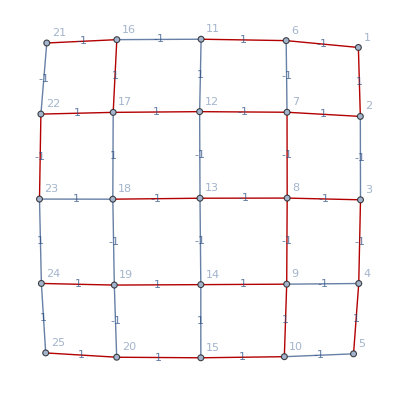

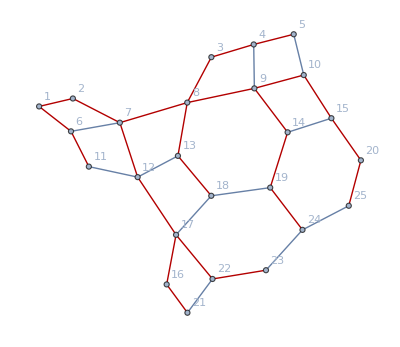

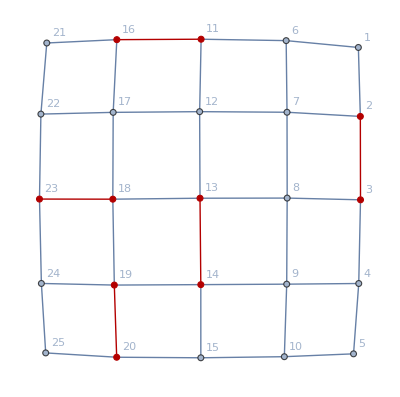

```mathematica
Reap[BreadthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],1,{"FrontierEdge"->Sow}]]⟦2,1⟧//HighlightGraph[%,#]&

Reap[BreadthFirstScan[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],1,{"FrontierEdge"->Sow}]]⟦2,1⟧//HighlightGraph[GraphDifference[labelEdges[lattice],Graph[listToEdges[latticeMinCut]]],#]&//labelVertices

HighlightGraph[lattice,Graph[listToEdges[latticeMinCut]]]//labelVertices
```

```mathematica
(*BFS for spinconf*)
```